```mathematica
ClearAll[px,rBlank,rPhase,x1,x2,tie,rPhasePlot,near,ytie1,xtie1,xtie2,lever,loc,tieline,sum1,sum2,y1];
```

```mathematica
Manipulate[
Module[{px,rBlank,rPhase,x1,x2,tie,rPhasePlot,near,ytie1,xtie1,xtie2,lever,loc,tieline,sum1,sum2,y1},
(*px=pt[[1]];py=pt[[2]];*)
px=0.3;

rBlank=Graphics[{{Thin,GrayLevel[0.65],Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.1}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
Text[Style["S",18],{1.03,0}],Text[Style["A",18],{0,1.025}],Text[Style["C",18],{-0.025,-0.025}]},PlotRange->{{-0.1,1.1},{-0.05,1.05}}];

rPhase=Interpolation[Table[BezierFunction[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}][i],{i,0,1,0.025}]];

x1=Table[x/.FindRoot[rPhase[x]==y,{x,0.1}],{y,{0.03,0.07,0.12,0.18,0.26,0.32}}];
x2=Table[x/.FindRoot[rPhase[x]==y,{x,0.9}],{y,{0.05,0.13,0.2,0.28,0.37,0.43}}];

tie[x_,n_]:=((rPhase[x2[[n]]]-rPhase[x1[[n]]])/(x2[[n]]-x1[[n]]))*(x-x1[[n]])+rPhase[x1[[n]]];

loc[c1_,c2_,c3_,c4_,c5_,c6_,c7_]:=Which[
py≤tie[px,1],c1,
tie[px,1]<py≤tie[px,2],c2,
tie[px,2]<py≤tie[px,3],c3,
tie[px,3]<py≤tie[px,4],c4,
tie[px,4]<py≤tie[px,5],c5,
tie[px,5]<py≤tie[px,6],c6,
tie[px,6]<py,c7];


(*xtie1=x/.FindRoot[rPhase[x]==(py*(loc[0.1,x1[[1]],x1[[2]],x1[[3]],x1[[4]],x1[[5]],x1[[6]]]+loc[x1[[1]],x1[[2]],x1[[3]],x1[[4]],x1[[5]],x1[[6]],0.22]))/loc[tie[px,1],tie[px,1]+tie[px,2],tie[px,2]+tie[px,3],tie[px,3]+tie[px,4],tie[px,4]+tie[px,5],tie[px,5]+tie[px,6],tie[px,6]+0.45],{x,0.1}];*)

sum1=Which[
py≤tie[px,1],tie[px,1],
tie[px,1]<py≤tie[px,2],tie[px,1]+tie[px,2],
tie[px,2]<py≤tie[px,3],tie[px,2]+tie[px,3],
tie[px,3]<py≤tie[px,4],tie[px,3]+tie[px,4],
tie[px,4]<py≤tie[px,5],tie[px,4]+tie[px,5],
tie[px,5]<py≤tie[px,6],tie[px,5]+tie[px,6],
tie[px,6]<py,tie[px,6]];

sum2=Which[
py≤tie[px,1],tie[0.05,1],
tie[px,1]<py≤tie[px,2],tie[0.05,1]+tie[0.13,2],
tie[px,2]<py≤tie[px,3],tie[0.13,2]+tie[0.2,3],
tie[px,3]<py≤tie[px,4],tie[0.2,3]+tie[0.28,4],
tie[px,4]<py≤tie[px,5],tie[0.28,4]+tie[0.37,5],
tie[px,5]<py≤tie[px,6],tie[0.37,5]+tie[0.43,6],
tie[px,6]<py,tie[0.43,6]];

y1=y/.FindRoot[py/(py+sum1)==y/(y+sum2),{y,0}];
(*xtie1=x/.FindRoot[rPhase[x]==py*sum2/sum1,{x,0.9}];*)
xtie1=x/.FindRoot[rPhase[x]==y1,{x,0.1}];

rPhasePlot=Show[
Plot[rPhase[x],{x,0.1,0.9},PlotStyle->{Thick,Black}],
Table[Plot[tie[x,n],{x,x1[[n]],x2[[n]]},PlotStyle->{Thick,Black}],{n,1,6}]];


Show[rBlank,rPhasePlot,
(*Graphics[{
{PointSize[0.025],Point[{px,py}]},
{Thick,Dashed,Line[{{xtie1,rPhase[xtie1]},{px,py}}]}
}],*)
ImageSize->{470,450}
]
],
(*Control[{{pt,{0.3,0.25}},Locator,Appearance->Graphics[{Disk[]},ImageSize->12]}]*)
Control[{{py,0.25,""},0,1,0.01,Appearance->"Labeled"}]
]
```

```mathematica
(*lever=Which[
py≤tie[px,1],py/tie[px,1],
tie[px,1]<py≤tie[px,2],(py-tie[px,1])/(tie[px,2]-tie[px,1]),
tie[px,2]<py≤tie[px,3],(py-tie[px,2])/(tie[px,3]-tie[px,2]),
tie[px,3]<py≤tie[px,4],(py-tie[px,3])/(tie[px,4]-tie[px,3]),
tie[px,4]<py≤tie[px,5],(py-tie[px,4])/(tie[px,5]-tie[px,4]),
tie[px,5]<py≤tie[px,6],(py-tie[px,5])/(tie[px,6]-tie[px,5]),
tie[px,6]<py,py-tie[px,6]
];*)
```

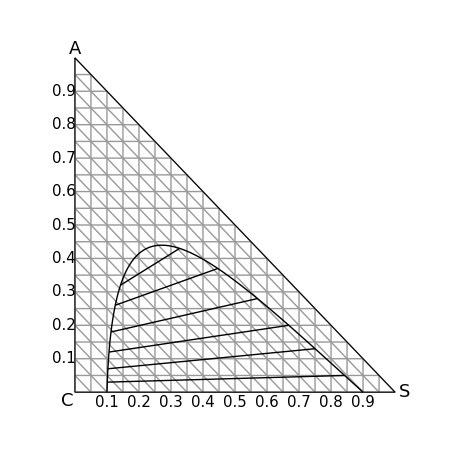

```mathematica
Module[{rBlank,rPhase,x1,x2,tie,rPhasePlot},
rBlank=Graphics[{{Thin,GrayLevel[0.6],Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
Text[Style["S",18],{1.03,0}],Text[Style["A",18],{0,1.025}],Text[Style["C",18],{-0.025,-0.025}]},PlotRange->{{-0.1,1.1},{-0.05,1.05}}];

rPhase=Interpolation[Table[BezierFunction[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}][i],{i,0,1,0.025}]];

x1=Table[x/.FindRoot[rPhase[x]==y,{x,0.1}],{y,{0.03,0.07,0.12,0.18,0.26,0.32}}];
x2=Table[x/.FindRoot[rPhase[x]==y,{x,0.9}],{y,{0.05,0.13,0.2,0.28,0.37,0.43}}];

tie[x_,n_]:=((rPhase[x2[[n]]]-rPhase[x1[[n]]])/(x2[[n]]-x1[[n]]))*(x-x1[[n]])+rPhase[x1[[n]]];

rPhasePlot=Show[
Plot[rPhase[x],{x,0.1,0.9},PlotStyle->{Thick,Black}],
Table[Plot[tie[x,n],{x,x1[[n]],x2[[n]]},PlotStyle->{Thick,Black}],{n,1,6}]];


Show[rBlank,rPhasePlot,ImageSize->{470,450}]
]
```